```mathematica
Mult[x_]:=(3x+1)
```

```mathematica
[x_]:=x/2
```

```mathematica
Mult[MyDiv[x]]==x//Solve
```

{{x→-2}}

```mathematica
Composition[Mult,MyDiv,MyDiv][x]
```

1+(3 x)/4

```mathematica
Solve[x/2==x]
```

{{x→0}}

```mathematica
MyPad[list_,n_]:=If[Length[list]<n,PadLeft[list,n],list]
```

```mathematica
ListToFunc[list_]:=Apply[Composition,Map[If[#==0,MyDiv,Mult]&,list]][x]
```

```mathematica
IntegerToList[n_]:=Apply[Composition,Map[If[#==0,MyDiv,Mult]&,IntegerDigits[n,2]]][x]
```

```mathematica
0
```

```mathematica
Collatz[n_]:=If[n==1,{n},If[EvenQ[n],Prepend[Collatz[n/2],n],Prepend[Collatz[3n+1],n]]]
```

```mathematica
Table[Collatz[k],{k,10}]
```

{{1},{2,1},{3,10,5,16,8,4,2,1},{4,2,1},{5,16,8,4,2,1},{6,3,10,5,16,8,4,2,1},{7,22,11,34,17,52,26,13,40,20,10,5,16,8,4,2,1},{8,4,2,1},{9,28,14,7,22,11,34,17,52,26,13,40,20,10,5,16,8,4,2,1},{10,5,16,8,4,2,1}}

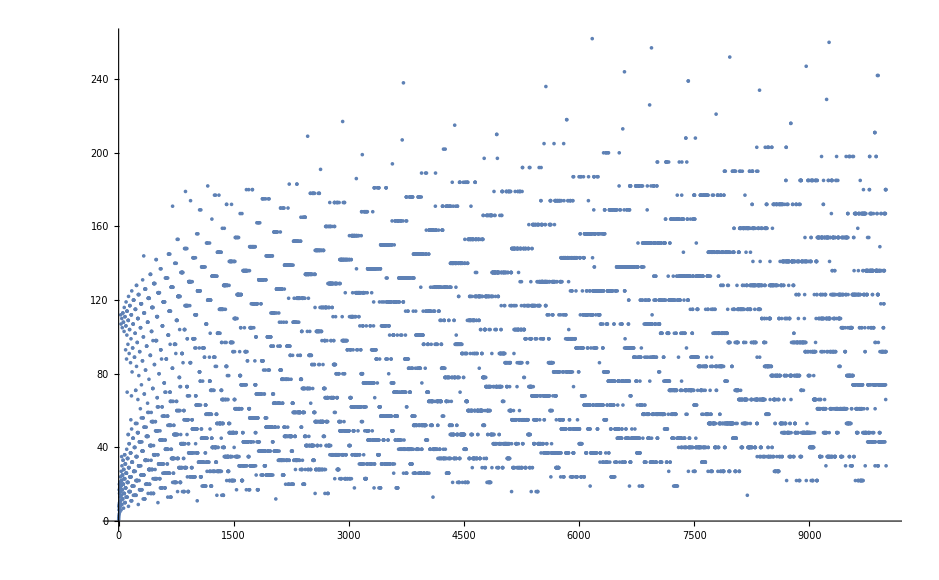

```mathematica
Table[{k,Length[Collatz[k]]},{k,10000}]//ListPlot
```

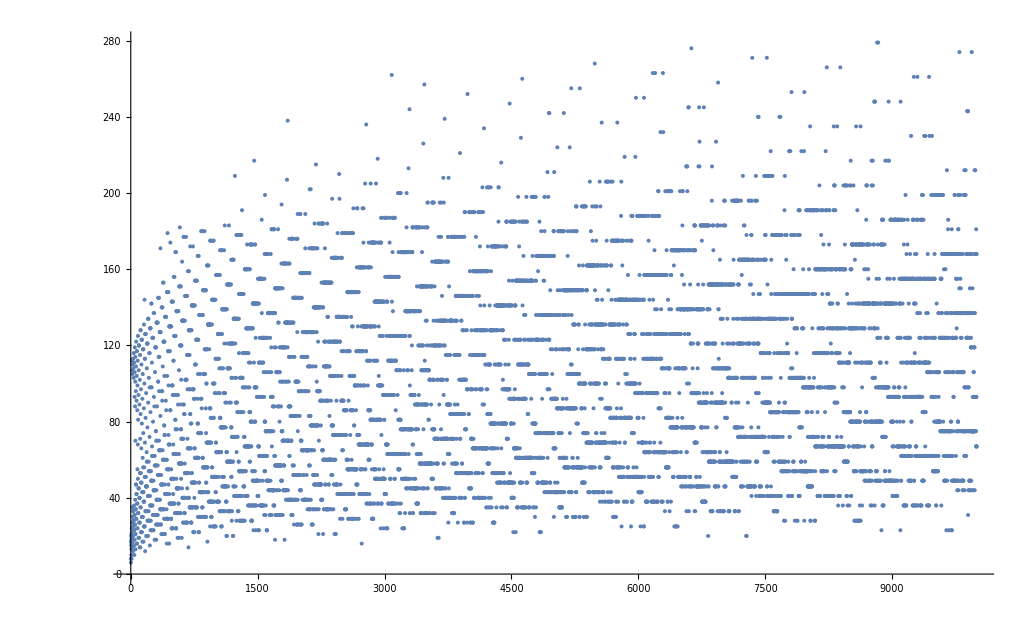

```mathematica
Table[{k,Length[Collatz[2k+1]]},{k,10000}]//ListPlot
```

```mathematica
IntegerDigits[5,2]
```

{1,0,1}

```mathematica
Collatz[5]
```

{5,16,8,4,2,1}

```mathematica
IntegerDigits[7,2]
```

{1,1,1}

```mathematica
Collatz[FromDigits[{1,1,1,0,0,0},2]]
```

{56,28,14,7,22,11,34,17,52,26,13,40,20,10,5,16,8,4,2,1}

```mathematica
Collatz[7]
```

{7,22,11,34,17,52,26,13,40,20,10,5,16,8,4,2,1}

```mathematica
Collatz[FromDigits[{1,0,1,0,0,0},2]]
```

{40,20,10,5,16,8,4,2,1}

```mathematica
Select[Range[100],First[Reverse[IntegerDigits[#,2]]]!=0&]
```

{1,3,5,7,9,11,13,15,17,19,21,23,25,27,29,31,33,35,37,39,41,43,45,47,49,51,53,55,57,59,61,63,65,67,69,71,73,75,77,79,81,83,85,87,89,91,93,95,97,99}

```mathematica
Table[With[{l=Table[1,{i,k}]},Factor[ListToFunc[l]]],{k,15}]
```

{1+3 x,4+9 x,13+27 x,40+81 x,121+243 x,364+729 x,1093+2187 x,3280+6561 x,9841+19683 x,29524+59049 x,88573+177147 x,265720+531441 x,797161+1594323 x,2391484+4782969 x,7174453+14348907 x}

```mathematica
PadLeft[IntegerDigits[70,2],3]
```

{1,1,0}

```mathematica
Table[{IntegerDigits[k,2],IntegerToList[k]//Factor},{k,70}]
```

{{{1},1+3 x},{{1,0},1/2 (2+3 x)},{{1,1},4+9 x},{{1,0,0},1/4 (4+3 x)},{{1,0,1},1/2 (5+9 x)},{{1,1,0},1/2 (8+9 x)},{{1,1,1},13+27 x},{{1,0,0,0},1/8 (8+3 x)},{{1,0,0,1},1/4 (7+9 x)},{{1,0,1,0},1/4 (10+9 x)},{{1,0,1,1},1/2 (14+27 x)},{{1,1,0,0},1/4 (16+9 x)},{{1,1,0,1},1/2 (17+27 x)},{{1,1,1,0},1/2 (26+27 x)},{{1,1,1,1},40+81 x},{{1,0,0,0,0},1/16 (16+3 x)},{{1,0,0,0,1},1/8 (11+9 x)},{{1,0,0,1,0},1/8 (14+9 x)},{{1,0,0,1,1},1/4 (16+27 x)},{{1,0,1,0,0},1/8 (20+9 x)},{{1,0,1,0,1},1/4 (19+27 x)},{{1,0,1,1,0},1/4 (28+27 x)},{{1,0,1,1,1},1/2 (41+81 x)},{{1,1,0,0,0},1/8 (32+9 x)},{{1,1,0,0,1},1/4 (25+27 x)},{{1,1,0,1,0},1/4 (34+27 x)},{{1,1,0,1,1},1/2 (44+81 x)},{{1,1,1,0,0},1/4 (52+27 x)},{{1,1,1,0,1},1/2 (53+81 x)},{{1,1,1,1,0},1/2 (80+81 x)},{{1,1,1,1,1},121+243 x},{{1,0,0,0,0,0},1/32 (32+3 x)},{{1,0,0,0,0,1},1/16 (19+9 x)},{{1,0,0,0,1,0},1/16 (22+9 x)},{{1,0,0,0,1,1},1/8 (20+27 x)},{{1,0,0,1,0,0},1/16 (28+9 x)},{{1,0,0,1,0,1},1/8 (23+27 x)},{{1,0,0,1,1,0},1/8 (32+27 x)},{{1,0,0,1,1,1},1/4 (43+81 x)},{{1,0,1,0,0,0},1/16 (40+9 x)},{{1,0,1,0,0,1},1/8 (29+27 x)},{{1,0,1,0,1,0},1/8 (38+27 x)},{{1,0,1,0,1,1},1/4 (46+81 x)},{{1,0,1,1,0,0},1/8 (56+27 x)},{{1,0,1,1,0,1},1/4 (55+81 x)},{{1,0,1,1,1,0},1/4 (82+81 x)},{{1,0,1,1,1,1},1/2 (122+243 x)},{{1,1,0,0,0,0},1/16 (64+9 x)},{{1,1,0,0,0,1},1/8 (41+27 x)},{{1,1,0,0,1,0},1/8 (50+27 x)},{{1,1,0,0,1,1},1/4 (52+81 x)},{{1,1,0,1,0,0},1/8 (68+27 x)},{{1,1,0,1,0,1},1/4 (61+81 x)},{{1,1,0,1,1,0},1/4 (88+81 x)},{{1,1,0,1,1,1},1/2 (125+243 x)},{{1,1,1,0,0,0},1/8 (104+27 x)},{{1,1,1,0,0,1},1/4 (79+81 x)},{{1,1,1,0,1,0},1/4 (106+81 x)},{{1,1,1,0,1,1},1/2 (134+243 x)},{{1,1,1,1,0,0},1/4 (160+81 x)},{{1,1,1,1,0,1},1/2 (161+243 x)},{{1,1,1,1,1,0},1/2 (242+243 x)},{{1,1,1,1,1,1},364+729 x},{{1,0,0,0,0,0,0},1/64 (64+3 x)},{{1,0,0,0,0,0,1},1/32 (35+9 x)},{{1,0,0,0,0,1,0},1/32 (38+9 x)},{{1,0,0,0,0,1,1},1/16 (28+27 x)},{{1,0,0,0,1,0,0},1/32 (44+9 x)},{{1,0,0,0,1,0,1},1/16 (31+27 x)},{{1,0,0,0,1,1,0},1/16 (40+27 x)}}

```mathematica
Table[{MyPad[IntegerDigits[k,2],3],Reduce[IntegerToList[k]==x]},{k,70}]
```

```mathematica
Table[{IntegerDigits[k,2]/.{0->MyDiv,1->Mult},Reduce[IntegerToList[k]==x]},{k,70}]
```

{{{Mult},x==-1/2},{{Mult,MyDiv},x==-2},{{Mult,Mult},x==-1/2},{{Mult,MyDiv,MyDiv},x==4},{{Mult,MyDiv,Mult},x==-5/7},{{Mult,Mult,MyDiv},x==-8/7},{{Mult,Mult,Mult},x==-1/2},{{Mult,MyDiv,MyDiv,MyDiv},x==8/5},{{Mult,MyDiv,MyDiv,Mult},x==-7/5},{{Mult,MyDiv,Mult,MyDiv},x==-2},{{Mult,MyDiv,Mult,Mult},x==-14/25},{{Mult,Mult,MyDiv,MyDiv},x==-16/5},{{Mult,Mult,MyDiv,Mult},x==-17/25},{{Mult,Mult,Mult,MyDiv},x==-26/25},{{Mult,Mult,Mult,Mult},x==-1/2},{{Mult,MyDiv,MyDiv,MyDiv,MyDiv},x==16/13},{{Mult,MyDiv,MyDiv,MyDiv,Mult},x==-11},{{Mult,MyDiv,MyDiv,Mult,MyDiv},x==-14},{{Mult,MyDiv,MyDiv,Mult,Mult},x==-16/23},{{Mult,MyDiv,Mult,MyDiv,MyDiv},x==-20},{{Mult,MyDiv,Mult,MyDiv,Mult},x==-19/23},{{Mult,MyDiv,Mult,Mult,MyDiv},x==-28/23},{{Mult,MyDiv,Mult,Mult,Mult},x==-41/79},{{Mult,Mult,MyDiv,MyDiv,MyDiv},x==-32},{{Mult,Mult,MyDiv,MyDiv,Mult},x==-25/23},{{Mult,Mult,MyDiv,Mult,MyDiv},x==-34/23},{{Mult,Mult,MyDiv,Mult,Mult},x==-44/79},{{Mult,Mult,Mult,MyDiv,MyDiv},x==-52/23},{{Mult,Mult,Mult,MyDiv,Mult},x==-53/79},{{Mult,Mult,Mult,Mult,MyDiv},x==-80/79},{{Mult,Mult,Mult,Mult,Mult},x==-1/2},{{Mult,MyDiv,MyDiv,MyDiv,MyDiv,MyDiv},x==32/29},{{Mult,MyDiv,MyDiv,MyDiv,MyDiv,Mult},x==19/7},{{Mult,MyDiv,MyDiv,MyDiv,Mult,MyDiv},x==22/7},{{Mult,MyDiv,MyDiv,MyDiv,Mult,Mult},x==-20/19},{{Mult,MyDiv,MyDiv,Mult,MyDiv,MyDiv},x==4},{{Mult,MyDiv,MyDiv,Mult,MyDiv,Mult},x==-23/19},{{Mult,MyDiv,MyDiv,Mult,Mult,MyDiv},x==-32/19},{{Mult,MyDiv,MyDiv,Mult,Mult,Mult},x==-43/77},{{Mult,MyDiv,Mult,MyDiv,MyDiv,MyDiv},x==40/7},{{Mult,MyDiv,Mult,MyDiv,MyDiv,Mult},x==-29/19},{{Mult,MyDiv,Mult,MyDiv,Mult,MyDiv},x==-2},{{Mult,MyDiv,Mult,MyDiv,Mult,Mult},x==-46/77},{{Mult,MyDiv,Mult,Mult,MyDiv,MyDiv},x==-56/19},{{Mult,MyDiv,Mult,Mult,MyDiv,Mult},x==-5/7},{{Mult,MyDiv,Mult,Mult,Mult,MyDiv},x==-82/77},{{Mult,MyDiv,Mult,Mult,Mult,Mult},x==-122/241},{{Mult,Mult,MyDiv,MyDiv,MyDiv,MyDiv},x==64/7},{{Mult,Mult,MyDiv,MyDiv,MyDiv,Mult},x==-41/19},{{Mult,Mult,MyDiv,MyDiv,Mult,MyDiv},x==-50/19},{{Mult,Mult,MyDiv,MyDiv,Mult,Mult},x==-52/77},{{Mult,Mult,MyDiv,Mult,MyDiv,MyDiv},x==-68/19},{{Mult,Mult,MyDiv,Mult,MyDiv,Mult},x==-61/77},{{Mult,Mult,MyDiv,Mult,Mult,MyDiv},x==-8/7},{{Mult,Mult,MyDiv,Mult,Mult,Mult},x==-125/241},{{Mult,Mult,Mult,MyDiv,MyDiv,MyDiv},x==-104/19},{{Mult,Mult,Mult,MyDiv,MyDiv,Mult},x==-79/77},{{Mult,Mult,Mult,MyDiv,Mult,MyDiv},x==-106/77},{{Mult,Mult,Mult,MyDiv,Mult,Mult},x==-134/241},{{Mult,Mult,Mult,Mult,MyDiv,MyDiv},x==-160/77},{{Mult,Mult,Mult,Mult,MyDiv,Mult},x==-161/241},{{Mult,Mult,Mult,Mult,Mult,MyDiv},x==-242/241},{{Mult,Mult,Mult,Mult,Mult,Mult},x==-1/2},{{Mult,MyDiv,MyDiv,MyDiv,MyDiv,MyDiv,MyDiv},x==64/61},{{Mult,MyDiv,MyDiv,MyDiv,MyDiv,MyDiv,Mult},x==35/23},{{Mult,MyDiv,MyDiv,MyDiv,MyDiv,Mult,MyDiv},x==38/23},{{Mult,MyDiv,MyDiv,MyDiv,MyDiv,Mult,Mult},x==-28/11},{{Mult,MyDiv,MyDiv,MyDiv,Mult,MyDiv,MyDiv},x==44/23},{{Mult,MyDiv,MyDiv,MyDiv,Mult,MyDiv,Mult},x==-31/11},{{Mult,MyDiv,MyDiv,MyDiv,Mult,Mult,MyDiv},x==-40/11}}

```mathematica
Select[Range[2000],With[{sol=x/.First[Solve[IntegerToList[#]==x,x]]},IntegerQ[sol]&&sol≥0]&]
```

{4,36,140,145,200,292,1059,1136,1553,1800}

```mathematica
First[Solve[IntegerToList[1800]==x,x]]
```

{x→40}

```mathematica
Table[With[{digs=IntegerDigits[k,2]},{digs,IntegerToList[k]//Factor,With[{ones=Length[Select[digs,#==1&]], zeroes=Length[Select[digs,#==0&]]},(1+x 3^ones )/2^zeroes],IntegerToList[k]==x//Reduce}],{k,70}]
```

{{{1},1+3 x,1+3 x,x==-1/2},{{1,0},1/2 (2+3 x),1/2 (1+3 x),x==-2},{{1,1},4+9 x,1+9 x,x==-1/2},{{1,0,0},1/4 (4+3 x),1/4 (1+3 x),x==4},{{1,0,1},1/2 (5+9 x),1/2 (1+9 x),x==-5/7},{{1,1,0},1/2 (8+9 x),1/2 (1+9 x),x==-8/7},{{1,1,1},13+27 x,1+27 x,x==-1/2},{{1,0,0,0},1/8 (8+3 x),1/8 (1+3 x),x==8/5},{{1,0,0,1},1/4 (7+9 x),1/4 (1+9 x),x==-7/5},{{1,0,1,0},1/4 (10+9 x),1/4 (1+9 x),x==-2},{{1,0,1,1},1/2 (14+27 x),1/2 (1+27 x),x==-14/25},{{1,1,0,0},1/4 (16+9 x),1/4 (1+9 x),x==-16/5},{{1,1,0,1},1/2 (17+27 x),1/2 (1+27 x),x==-17/25},{{1,1,1,0},1/2 (26+27 x),1/2 (1+27 x),x==-26/25},{{1,1,1,1},40+81 x,1+81 x,x==-1/2},{{1,0,0,0,0},1/16 (16+3 x),1/16 (1+3 x),x==16/13},{{1,0,0,0,1},1/8 (11+9 x),1/8 (1+9 x),x==-11},{{1,0,0,1,0},1/8 (14+9 x),1/8 (1+9 x),x==-14},{{1,0,0,1,1},1/4 (16+27 x),1/4 (1+27 x),x==-16/23},{{1,0,1,0,0},1/8 (20+9 x),1/8 (1+9 x),x==-20},{{1,0,1,0,1},1/4 (19+27 x),1/4 (1+27 x),x==-19/23},{{1,0,1,1,0},1/4 (28+27 x),1/4 (1+27 x),x==-28/23},{{1,0,1,1,1},1/2 (41+81 x),1/2 (1+81 x),x==-41/79},{{1,1,0,0,0},1/8 (32+9 x),1/8 (1+9 x),x==-32},{{1,1,0,0,1},1/4 (25+27 x),1/4 (1+27 x),x==-25/23},{{1,1,0,1,0},1/4 (34+27 x),1/4 (1+27 x),x==-34/23},{{1,1,0,1,1},1/2 (44+81 x),1/2 (1+81 x),x==-44/79},{{1,1,1,0,0},1/4 (52+27 x),1/4 (1+27 x),x==-52/23},{{1,1,1,0,1},1/2 (53+81 x),1/2 (1+81 x),x==-53/79},{{1,1,1,1,0},1/2 (80+81 x),1/2 (1+81 x),x==-80/79},{{1,1,1,1,1},121+243 x,1+243 x,x==-1/2},{{1,0,0,0,0,0},1/32 (32+3 x),1/32 (1+3 x),x==32/29},{{1,0,0,0,0,1},1/16 (19+9 x),1/16 (1+9 x),x==19/7},{{1,0,0,0,1,0},1/16 (22+9 x),1/16 (1+9 x),x==22/7},{{1,0,0,0,1,1},1/8 (20+27 x),1/8 (1+27 x),x==-20/19},{{1,0,0,1,0,0},1/16 (28+9 x),1/16 (1+9 x),x==4},{{1,0,0,1,0,1},1/8 (23+27 x),1/8 (1+27 x),x==-23/19},{{1,0,0,1,1,0},1/8 (32+27 x),1/8 (1+27 x),x==-32/19},{{1,0,0,1,1,1},1/4 (43+81 x),1/4 (1+81 x),x==-43/77},{{1,0,1,0,0,0},1/16 (40+9 x),1/16 (1+9 x),x==40/7},{{1,0,1,0,0,1},1/8 (29+27 x),1/8 (1+27 x),x==-29/19},{{1,0,1,0,1,0},1/8 (38+27 x),1/8 (1+27 x),x==-2},{{1,0,1,0,1,1},1/4 (46+81 x),1/4 (1+81 x),x==-46/77},{{1,0,1,1,0,0},1/8 (56+27 x),1/8 (1+27 x),x==-56/19},{{1,0,1,1,0,1},1/4 (55+81 x),1/4 (1+81 x),x==-5/7},{{1,0,1,1,1,0},1/4 (82+81 x),1/4 (1+81 x),x==-82/77},{{1,0,1,1,1,1},1/2 (122+243 x),1/2 (1+243 x),x==-122/241},{{1,1,0,0,0,0},1/16 (64+9 x),1/16 (1+9 x),x==64/7},{{1,1,0,0,0,1},1/8 (41+27 x),1/8 (1+27 x),x==-41/19},{{1,1,0,0,1,0},1/8 (50+27 x),1/8 (1+27 x),x==-50/19},{{1,1,0,0,1,1},1/4 (52+81 x),1/4 (1+81 x),x==-52/77},{{1,1,0,1,0,0},1/8 (68+27 x),1/8 (1+27 x),x==-68/19},{{1,1,0,1,0,1},1/4 (61+81 x),1/4 (1+81 x),x==-61/77},{{1,1,0,1,1,0},1/4 (88+81 x),1/4 (1+81 x),x==-8/7},{{1,1,0,1,1,1},1/2 (125+243 x),1/2 (1+243 x),x==-125/241},{{1,1,1,0,0,0},1/8 (104+27 x),1/8 (1+27 x),x==-104/19},{{1,1,1,0,0,1},1/4 (79+81 x),1/4 (1+81 x),x==-79/77},{{1,1,1,0,1,0},1/4 (106+81 x),1/4 (1+81 x),x==-106/77},{{1,1,1,0,1,1},1/2 (134+243 x),1/2 (1+243 x),x==-134/241},{{1,1,1,1,0,0},1/4 (160+81 x),1/4 (1+81 x),x==-160/77},{{1,1,1,1,0,1},1/2 (161+243 x),1/2 (1+243 x),x==-161/241},{{1,1,1,1,1,0},1/2 (242+243 x),1/2 (1+243 x),x==-242/241},{{1,1,1,1,1,1},364+729 x,1+729 x,x==-1/2},{{1,0,0,0,0,0,0},1/64 (64+3 x),1/64 (1+3 x),x==64/61},{{1,0,0,0,0,0,1},1/32 (35+9 x),1/32 (1+9 x),x==35/23},{{1,0,0,0,0,1,0},1/32 (38+9 x),1/32 (1+9 x),x==38/23},{{1,0,0,0,0,1,1},1/16 (28+27 x),1/16 (1+27 x),x==-28/11},{{1,0,0,0,1,0,0},1/32 (44+9 x),1/32 (1+9 x),x==44/23},{{1,0,0,0,1,0,1},1/16 (31+27 x),1/16 (1+27 x),x==-31/11},{{1,0,0,0,1,1,0},1/16 (40+27 x),1/16 (1+27 x),x==-40/11}}

```mathematica
Table[{MyPad[IntegerDigits[k,2],3],IntegerToList[k]//Factor},{k,70}]
```

```mathematica
Select[Range[100],IntegerQ[Last[Last[Solve[IntegerToList[#]==x,x]]]]&]
```

{}

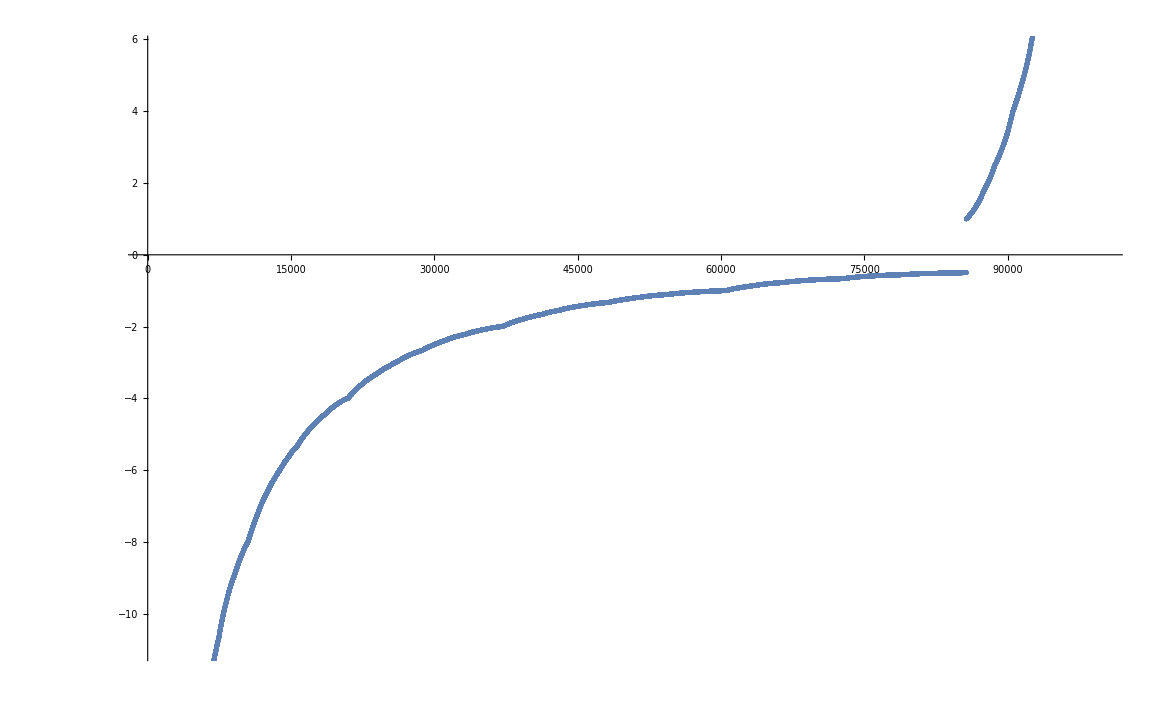

```mathematica
Table[x/.Last[Last[Solve[IntegerToList[k]==x,x]]],{k,100000}]//Sort//ListPlot
```

```mathematica
Select[Table[x/.Last[Last[Solve[IntegerToList[k]==x,x]]],{k,10}],#<0&]//Max
```

-1/2

```mathematica
Select[Table[x/.Last[Last[Solve[IntegerToList[k]==x,x]]],{k,100}],#<0&]//Max
```

```mathematica
Table[Select[Table[x/.Last[Last[Solve[IntegerToList[k]==x,x]]],{k,2^m}],#<0&]//Max,{m,13}]
```

{-1/2,-1/2,-1/2,-1/2,-1/2,-1/2,-1/2,-1/2,-1/2,-1/2,-1/2,-1/2,-1/2}

```mathematica
Select[Table[x/.Last[Last[Solve[IntegerToList[k]==x,x]]],{k,100}],#==0&]
```

{}

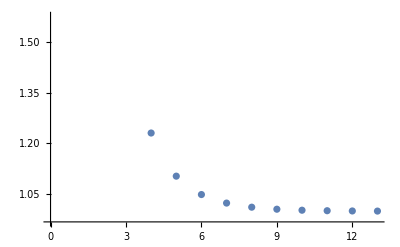

```mathematica
Table[Select[Table[x/.Last[Last[Solve[IntegerToList[k]==x,x]]],{k,2^m}],#>0&]//Min,{m,13}]//ListPlot
```

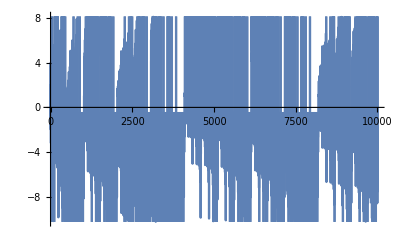

```mathematica
Table[x/.Last[Last[Solve[IntegerToList[k]==x,x]]],{k,10000}]//ListLinePlot
```

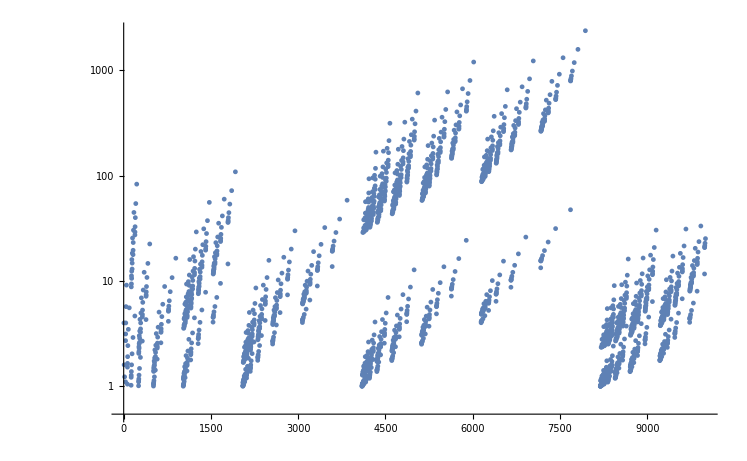

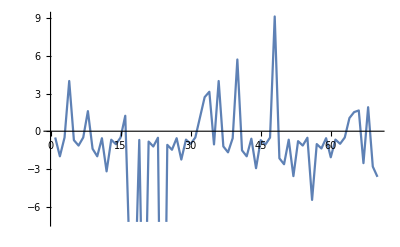

```mathematica
ListLogPlot[Table[{k,x/.Last[Last[Solve[IntegerToList[k]==x,x]]]},{k,10000}],PlotRange->All]
```